```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_,y_] := x^2+y^2+x y - 3
g[x_,y_]:=(x-1)^2+ (y-1)^2-x y^2-3
```

```mathematica
Plot3D[{f[x,y],g[x,y],0}, {x,-4,4}, {y,-4,4}, BoxRatios-> {1,1,1},AxesLabel->Automatic]
```

-Graphics3D-

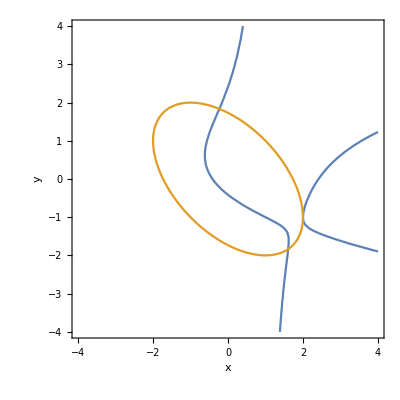

```mathematica
ContourPlot[{g[x,y] == 0, f[x,y] == 0}, {x,-4,4},{y,-4,4}, AxesLabel-> Automatic]
```

```mathematica
Subscript[f, x][x_,y_]:=D[f[x,y],x]
Subscript[f, y][x_,y_]:=D[f[x,y],y]
```

```mathematica
Subscript[g, x][x_,y_]:=D[g[x,y],x]
Subscript[g, y][x_,y_]:=D[g[x,y],y]
```

```mathematica
(*
解方程组：
	 f[Subscript[x, k],Subscript[y, k]] + (Subscript[x, k+1]-Subscript[x, k])Subscript[f, x][Subscript[x, k],Subscript[y, k]] + (Subscript[y, k+1]-Subscript[y, k])Subscript[f, y][Subscript[x, k],Subscript[y, k]] == 0 
  
 g[Subscript[x, k],Subscript[y, k]] + (Subscript[x, k+1]-Subscript[x, k])Subscript[g, x][Subscript[x, k],Subscript[y, k]] + (Subscript[y, k+1]-Subscript[y, k])Subscript[g, y][Subscript[x, k],Subscript[y, k]] == 0


 x = x + (f(x,y)Subscript[g, y](x,y)-g(x,y)Subscript[f, y](x,y))/(Subscript[g, x](x,y)Subscript[f, y](x,y)-Subscript[f, x](x,y)Subscript[g, y](x,y))
y = y + (g(x,y)Subscript[f, x](x,y)-f(x,y)Subscript[g, x](x,y))/(Subscript[g, x](x,y)Subscript[f, y](x,y)-Subscript[f, x](x,y)Subscript[g, y](x,y))
到达任意一个函数的极值时无法再次更新
*)
```

```mathematica
Solve[f[x,y] + (Nx-x)Subscript[f, x][x,y] + (Ny-y)Subscript[f, y][x,y]  == 0 &&g[x,y] + (Nx-x)Subscript[g, x][x,y] + (Ny-y)Subscript[g, y][x,y] == 0,{Nx,Ny}]
```

{{Nx→-(-6-x-2 x^2-x^3+4 y-8 x y-2 x^3 y-2 y^2+x y^2+2 x y^3)/(2 x+2 x^2-2 y+4 x^2 y-2 y^2+x y^2-2 y^3),Ny→-(6-4 x+2 x^2+y+2 x y-x^2 y+5 y^2-3 x^2 y^2+y^3-x y^3+y^4)/(2 x+2 x^2-2 y+4 x^2 y-2 y^2+x y^2-2 y^3)}}

```mathematica
Ax[x_,y_]:=(6+x+2 x^2+x^3-4 y+8 x y+2 x^3 y+2 y^2-x y^2-2 x y^3)/(2 x+2 x^2-2 y+4 x^2 y-2 y^2+x y^2-2 y^3)
Ay[x_,y_]:=(6-4 x+2 x^2+y+2 x y-x^2 y+5 y^2-3 x^2 y^2+y^3-x y^3+y^4)/(-2 x-2 x^2+2 y-4 x^2 y+2 y^2-x y^2+2 y^3)
```

```mathematica
pointList[x_,y_]:=N[NestWhileList[{Ax[#[[1]],#[[2]]],Ay[#[[1]],#[[2]]]}&,{x,y},Abs[#1[[1]]-#2[[1]]]>10^-5|| Abs[#1[[2]]-#2[[2]]]>10^-5&,2]]
```

```mathematica
plotPoint[u_,v_]:=Show[ListPlot[pointList[u,v],PlotStyle->Pink,PlotMarkers->{Automatic,Medium}],ContourPlot[{g[x,y] == 0, f[x,y] == 0}, {x,-4,4},{y,-4,4}, AxesLabel-> Automatic],PlotRange->{{u-0.5,u+0.5},{v-0.5,v+0.5}}]
```

```mathematica
ContourPlot[{g[x,y] == 0, f[x,y] == 0}, {x,-4,4},{y,-4,4}, AxesLabel-> Automatic]
```

-Graphics-

{{0.,2.},{-0.214286,1.85714},{-0.231856,1.83662},{-0.232048,1.83638},{-0.232048,1.83638}}

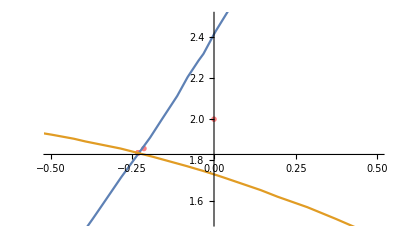

```mathematica
pointList[0,2]
plotPoint[0,2]
```

{{1.5,-2.},{1.58333,-1.86667},{1.60323,-1.83797},{1.60433,-1.83638},{1.60433,-1.83638}}

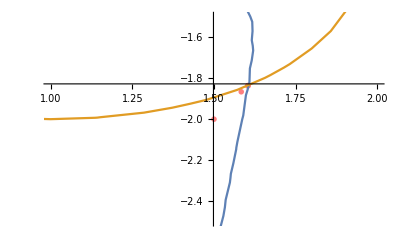

```mathematica
pointList[1.5,-2]
plotPoint[1.5,-2]
```

{{2.,-1.5},{2.,-1.25},{2.,-1.125},{2.,-1.0625},{2.,-1.03125},{2.,-1.01563},{2.,-1.00781},{2.,-1.00391},{2.,-1.00195},{2.,-1.00098},{2.,-1.00049},{2.,-1.00024},{2.,-1.00012},{2.,-1.00006},{2.,-1.00003},{2.,-1.00002},{2.,-1.00001}}

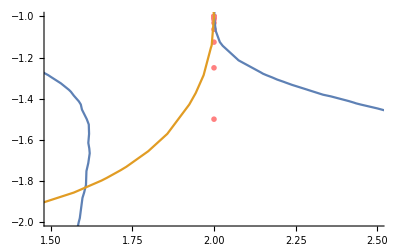

```mathematica
pointList[2,-1.5]
plotPoint[2,-1.5]
```

{{2.,-0.5},{2.,-0.75},{2.,-0.875},{2.,-0.9375},{2.,-0.96875},{2.,-0.984375},{2.,-0.992188},{2.,-0.996094},{2.,-0.998047},{2.,-0.999023},{2.,-0.999512},{2.,-0.999756},{2.,-0.999878},{2.,-0.999939},{2.,-0.999969},{2.,-0.999985},{2.,-0.999992}}

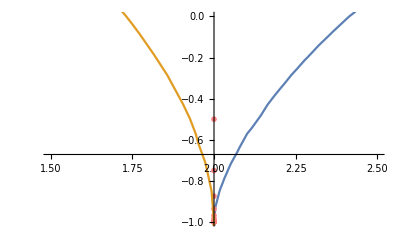

```mathematica
pointList[2,-0.5]
plotPoint[2,-0.5]
```

{{1.5,-1.},{2.0625,-1.25},{1.99559,-1.14503},{2.00032,-1.0706},{1.99999,-1.03541},{2.,-1.0177},{2.,-1.00885},{2.,-1.00443},{2.,-1.00221},{2.,-1.00111},{2.,-1.00055},{2.,-1.00028},{2.,-1.00014},{2.,-1.00007},{2.,-1.00003},{2.,-1.00002},{2.,-1.00001}}

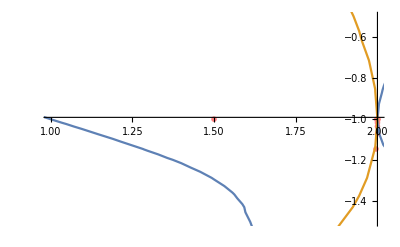

```mathematica
pointList[1.5,-1]
plotPoint[1.5,-1]
```

{{2.4,-1.2},{2.03333,-1.08627},{1.99958,-1.04983},{2.00001,-1.02477},{2.,-1.01239},{2.,-1.00619},{2.,-1.0031},{2.,-1.00155},{2.,-1.00077},{2.,-1.00039},{2.,-1.00019},{2.,-1.0001},{2.,-1.00005},{2.,-1.00002},{2.,-1.00001},{2.,-1.00001}}

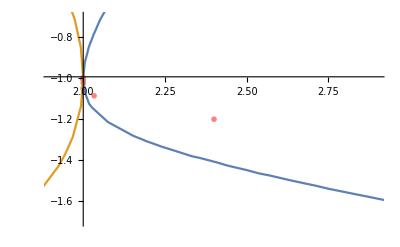

```mathematica
pointList[2.4,-1.2]
plotPoint[2.4,-1.2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{{2.,-1.},{Indeterminate,Indeterminate}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

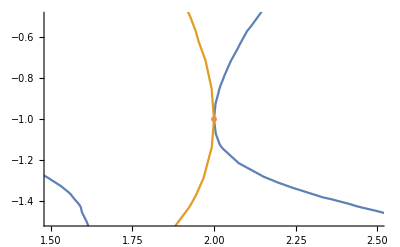

```mathematica
pointList[2,-1]
plotPoint[2,-1]
```

```mathematica
Plot3D[{f[x,y],g[x,y],0},{x,1.9,2.1},{y,-1.1,-0.9},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*
迭代公式：
	x = x + (f(x,y)Subscript[g, y](x,y)-g(x,y)Subscript[f, y](x,y))/(Subscript[g, x](x,y)Subscript[f, y](x,y)-Subscript[f, x](x,y)Subscript[g, y](x,y))
y = y + (g(x,y)Subscript[f, x](x,y)-f(x,y)Subscript[g, x](x,y))/(Subscript[g, x](x,y)Subscript[f, y](x,y)-Subscript[f, x](x,y)Subscript[g, y](x,y))
*)
```

```mathematica
NSolve[f[x,y]==0 && g[x,y] ==0, {x,y},Reals]
```

{{x→1.60433,y→-1.83638},{x→2.,y→-1.},{x→2.,y→-1.},{x→-0.232048,y→1.83638}}

```mathematica
Plot3D[{f[x,y],g[x,y],0}, {x,-4,4}, {y,-4,4}, BoxRatios-> {1,1,1},AxesLabel->Automatic]
```

-Graphics3D-